# Math 223: Homework 8

Hardeep Bassi

04/07/2023

## Problem 1

Find the asymptotic behavior of , as  up to terms involving 
From lecture, we know that integration by parts works well on 
when is monotonic on the given interval. Since , we satisfy this criterion, hence we obtain:
. Using this formula for the first two terms yields:
. To check this approximation we see:

```mathematica
approx[x_] = (-I*(2+Sin[2])*E^(2*I*x))/x + (E^(2*I*x)*(Cos[2]+1))/x^2 - 2/x^2
```

-2/x^2+(ⅇ^(2 ⅈ x) (1+Cos[2]))/x^2-(ⅈ ⅇ^(2 ⅈ x) (2+Sin[2]))/x

```mathematica
exact[x_] = Integrate[(Sin[t] + t) * E^(I*x*t), {t,0,2}]
```

(-1+ⅇ^(2 ⅈ x) (1-2 ⅈ x))/x^2+(-1+ⅇ^(2 ⅈ x) (Cos[2]-ⅈ x Sin[2]))/(-1+x^2)

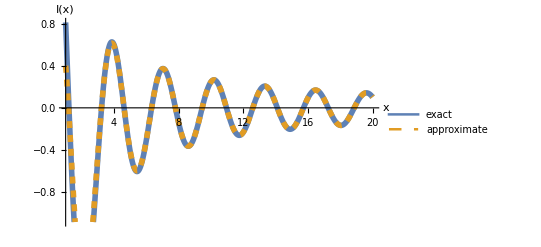

```mathematica
Plot[{Re[exact[x]], Re[approx[x]]},{x,1,20},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

We see agreement between the exact and the approximate solution as , so we appear to be good to go.

## Problem 2

Find the leading behavior of .
We seek to put this integral in the form to invoke Watson’s lemma. To start, we reformulate as:
. Letting , we get:
. To obtain 0 as our lower bound, we substitute  to obtain:
. By Watson’s, we get:

```mathematica
Series[a*E^w*((a*E^w-a)*(1+a-a*E^w))^(1/2),{w,0,3},Assumptions->a>0]
```

a^(3/2) √w-1/4 (a (-5 √a+2 a^(3/2))) w^(3/2)-1/96 (a (-77 √a+84 a^(3/2)+12 a^(5/2))) w^(5/2)+O[w]^(7/2)

```mathematica
approx[x_,a_] = a^(-x)*Integrate[(a^(3/2) √w-1/4 (a (-5 √a+2 a^(3/2))) w^(3/2))*E^(-x*w),{w,0,Infinity},Assumptions->x>0 && a > 0]
```

(a^(3/2-x) √π (15-6 a+8 x))/(16 x^(5/2))

```mathematica
exact[x_,a_]=Integrate[(t(1-t))^(1/2)(t+a)^(-x),{t,0,1},Assumptions->x>0 && a > 0]
```

1/(4 (-2+x) (-1+x))a^-x π (a (1+2 a) Hypergeometric2F1[-1/2,x,1,-1/a]-(1+a) (-1+2 a+2 x) Hypergeometric2F1[1/2,x,1,-1/a])

```mathematica
Manipulate[Plot[{exact[x,a],approx[x,a]},{x,1,50},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact","asymptotic approximation"}],{a,0.1,10}]
```

## Problem 3

Use the method of stationary phase to find the leading behaviors of the follow integrals as .
(a) 
Let . This yields the integral:

 Here, we see that  and . This means that the stationary point is given when  Hence, by the relation from lecture on a boundary point of: I(x) ∼ 1/2((2 π)/(x|ϕ''(a)|))^(1/2)f(a) ⅇ^(ⅈ x ϕ(a)+ⅈ π sgn(ϕ''(a))/4),   x→+∞ we have that:

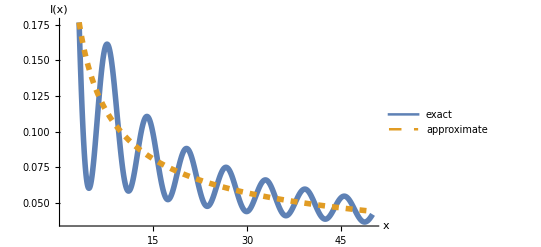

```mathematica
Plot[{Re[NIntegrate[Tan[t]*E^(I*x*(t^4)), {t,0,1}]],Re[(1/4)*(Pi/x)^(1/2)*E^(I*Pi/4) ]},{x,1,50},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

(b) .
As before, we take . This means we have , since we are only concerned with the values within our bounds of integration. Since this is not an end point, we use:
I(x) ∼ ((2 π)/(x|ϕ''(a)|))^(1/2)f(a) ⅇ^(ⅈ x ϕ(a)+ⅈ π sgn(ϕ''(a))/4),   x→+∞ . This yields:

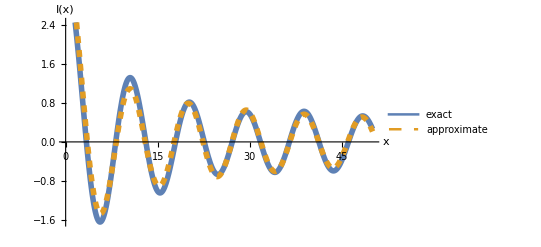

```mathematica
Plot[{Re[NIntegrate[(1+t)*E^(I*x*(t^3/3 -t)), {t,1/2,2}]],Re[2 * (Pi/x)^(1/2)*E^((-2*I*x)/3 + (I*Pi/4)) ]},{x,0,50},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

(c) 
Here, we recognize that the cosine term can be treated as the real part of the imaginary exponential expansion .  This means we can harness the solution of 3a by:
. Hence we get:

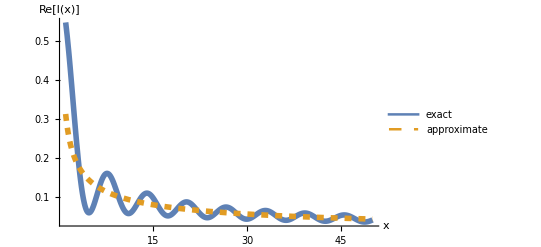

```mathematica
Plot[{Re[NIntegrate[Cos[x*t^4]*Tan[t],{t,0,1}]],Re[(1/4)*(Pi/x)^(1/2)*E^(I*Pi/4) ]},{x,1,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Re[I(x)]", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact","approximate"}]
```